```mathematica
θ[x_]:=If[x>0, 1, 0]
```

```mathematica
θ[-4]
```

0

```mathematica
f[x_, a_, b_, c1_, c2_]:= c1 θ[a - x] + θ[x-a]θ[b - x] ((c2 - c1)/(b -a)(x-a)+c1)+ c2 θ[x - b]
```

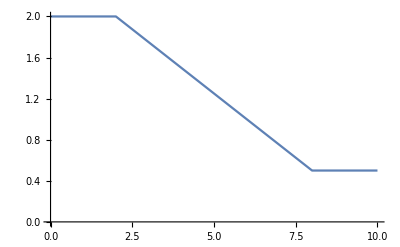

```mathematica
Plot[f[x, 2, 8, 2, 0.5], {x, 0, 10}, PlotRange->{0, 2}]
```